# Learning MNIST

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
data=ResourceData["MNIST"];
examples=[Binarize[First[#]]->Last[#]&,data];
effectiveExamples=examples;
```

```mathematica
smallExamples=[ImageResize[First[#],{8,8}]->Last[#]&,examples];
first4Digits=24754;
effectiveExamples=Take[smallExamples,first4Digits];
```

```mathematica
inputSize=Fold[Times,1,ImageDimensions[First[First[effectiveExamples]]]];
classes=DeleteDuplicates[Last/@effectiveExamples];
```

```mathematica
{trainData,testData}=[effectiveExamples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
Take[trainData,20]
```

{-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→0,-Graphics-→1,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→2,-Graphics-→3,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→0,-Graphics-→2,-Graphics-→2,-Graphics-→0,-Graphics-→1}

## Create feature encoders

```mathematica
inputEncoder=NetEncoder[{"Function",Flatten[ImageData[#]]&,{inputSize}}];
targetEncoder=NetEncoder[{"Class",classes,"IndicatorVector"}];
```

## Create net

```mathematica
{net,hardNet}=With[{classificationLayerSize=512*Length[classes]},
HardNeuralChain[{
HardNeuralAND[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,Length[classes]]
}]];
```

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,2048*Length[classes]],
HardNeuralAND[2048*Length[classes],256*Length[classes]],
HardNeuralNOT[256*Length[classes],Length[classes]]
}];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{"Net"->"Loss"},"Input"->inputEncoder,"Target"->targetEncoder
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[targetEncoder]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

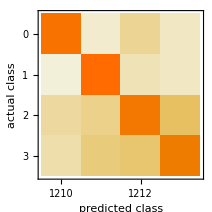
{Classifier Measurements
Classifier method | Net
Number of test examples | 4951
Accuracy | (94.140.33) %
Accuracy baseline | (25.90.6) %
Geometric mean of probabilities | 0.761 ± 0.015
Mean cross entropy | 0.274 ± 0.019
Single evaluation time | 4.77 ms/example
Batch evaluation speed | 869. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 4951
Accuracy | (94.140.33) %
Accuracy baseline | (25.90.6) %
Geometric mean of probabilities | 0.761 ± 0.015
Mean cross entropy | 0.274 ± 0.019
Single evaluation time | 6.19 ms/example
Batch evaluation speed | 892. examples/s
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,RandomSample[testData,UpTo[1000]],NetDecoder[targetEncoder],inputEncoder[First[#]]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.949

```mathematica
hncwt2=[Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&,testData];
```

```mathematica
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.941628

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

16. kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Standard net

```mathematica
classifier=Classify[trainData,Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

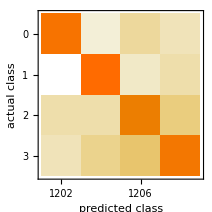
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 4951
Accuracy | (94.450.33) %
Accuracy baseline | (25.90.6) %
Geometric mean of probabilities | 0.845 ± 0.0085
Mean cross entropy | 0.169 ± 0.01
Single evaluation time | 6.31 ms/example
Batch evaluation speed | 21.2 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

480. kB